```mathematica
Δ=2Pi*4*10^6
```

8000000 π

```mathematica
Ω=2Pi*4*10^6
```

8000000 π

```mathematica
hbar=1.054571817*10^(-34)
```

1.05457×10^-34

```mathematica
h0=hbar*Δ/2
```

1.32521×10^-27

```mathematica
hc=hbar*Ω/2
```

1.32521×10^-27

```mathematica
d=4.6
```

4.6

```mathematica
Integrate[1/l/Sqrt[Pi] E^(-z^2/l^2),{z,-Infinity,Infinity},Assumptions->{l>0}]
```

1

```mathematica
eq=hc(Sqrt[(1-v0)/v0]-Sqrt[v0/(1-v0)])+2 hbar gd (2v0-1)==2h0
```

2.10914×10^-34 gd (-1+2 v0)+1.32521×10^-27 (√((1-v0)/v0)-√(v0/(1-v0)))==2.65043×10^-27

```mathematica
NSolve[eq/.{gd->10^6},v0,Reals]
```

{{v0→0.136655}}

```mathematica
solve[x_]:=v0/.NSolve[eq/.{gd->x},v0,Reals][[1]]
```

```mathematica
solve[10^6]
```

0.136655

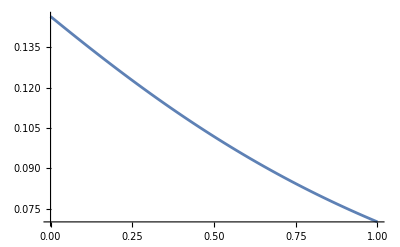

```mathematica
Plot[solve[gd],{gd,0,10^7}]
```